```mathematica
(*Example 10 map from Article, see article_example10.m (Matlab) for numerical calculation*)
A1={{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}};
A2={{0,0,1,0},{0,2,0,1},{1,0,2,0},{0,1,0,0}};
A3={{0,0,0,1},{0,-1,1,0},{0,1,1,0},{1,0,0,0}};
A4=IdentityMatrix[4];
A={A1,A2,A3,A4};
A1//MatrixForm
A2//MatrixForm
A3//MatrixForm
A4//MatrixForm
(* defining y=f(x) *)
y1={x1, x2, x3,x4}.A1.{x1,x2,x3,x4};
y2={x1, x2, x3,x4}.A2.{x1,x2,x3,x4};
y3={x1, x2, x3,x4}.A3.{x1,x2,x3,x4};
y4={x1, x2, x3,x4}.A4.{x1,x2,x3,x4};
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

(0 | 0 | 1 | 0
0 | 2 | 0 | 1
1 | 0 | 2 | 0
0 | 1 | 0 | 0)

(0 | 0 | 0 | 1
0 | -1 | 1 | 0
0 | 1 | 1 | 0
1 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(* Taking the solution x(Y), replacing root with List, taking the polynomial out. |x|=1 equivalent to y4=1, y3=0 -- required section *)
S = Solve[y1==Y1 && y2 ==Y2 && y3 ==0&&y4==1 , {x1, x2, x3,x4}] 
(*Poly:=((List @@ (x1/.S[[1]]))[[1]])*)
```

{{x1→(2891+1-17633828628725760 Y2^17 Root[1&,1]^(15/2))/(-21771583488 Y1^5+90311491584 Y1^6+543702122496 Y1^7-2146113552384 Y1^8-6230082191360 Y1^9+21101197819904 Y1^10+448+4121940261696 Y1 Y2^22+3199036688816 Y1^2 Y2^22-182521675136 Y2^23-297981538240 Y1 Y2^23+12456203392 Y2^24),x2→-√Root[16 Y1^6-72 Y1^7+42+10616832 #1^8&,1],x3→1/1,x4→(2887+1)/(463+1-12456203392 Y2^24)},{1},12,{1},{1}}
 |  |  |  |

```mathematica
(* Care about the boundary -> taking discriminant *)
Poly=(List@@(List@@(List @@ (x2/.S[[1]]))[[2]])[[1]])[[1]]
Quq=Discriminant[Poly[z], z];
```

16 Y1^6-72 Y1^7+81 Y1^8-64 Y1^4 Y2+272 Y1^5 Y2-192 Y1^6 Y2-216 Y1^7 Y2+64 Y1^2 Y2^2-256 Y1^3 Y2^2-32 Y1^4 Y2^2+520 Y1^5 Y2^2+324 Y1^6 Y2^2+192 Y1^2 Y2^3-224 Y1^3 Y2^3-576 Y1^4 Y2^3-312 Y1^5 Y2^3+80 Y1^2 Y2^4+360 Y1^3 Y2^4+214 Y1^4 Y2^4+16 Y1 Y2^5-128 Y1^2 Y2^5-104 Y1^3 Y2^5+24 Y1 Y2^6+36 Y1^2 Y2^6-8 Y1 Y2^7+Y2^8+(-256 Y1^2+1024 Y1^3-384 Y1^4-2048 Y1^5+736 Y1^6+1472 Y1^7-768 Y1^2 Y2+768 Y1^3 Y2+5248 Y1^4 Y2-5376 Y1^5 Y2-2800 Y1^6 Y2-256 Y2^2+1024 Y1 Y2^2-3072 Y1^2 Y2^2+1152 Y1^3 Y2^2+3744 Y1^4 Y2^2+1728 Y1^5 Y2^2-768 Y2^3+768 Y1 Y2^3-256 Y1^2 Y2^3+1280 Y1^3 Y2^3-304 Y1^4 Y2^3-128 Y2^4-2688 Y1 Y2^4-1632 Y1^2 Y2^4+192 Y1^3 Y2^4+640 Y2^5-144 Y1^2 Y2^5-32 Y2^6+192 Y1 Y2^6-80 Y2^7) #1+(1024-4096 Y1+10240 Y1^2-8192 Y1^3-17088 Y1^4+17536 Y1^5+6080 Y1^6+4096 Y2-7168 Y1 Y2+2048 Y1^2 Y2+10240 Y1^3 Y2-28032 Y1^4 Y2+5888 Y1^5 Y2+12288 Y2^2-9216 Y1 Y2^2+16512 Y1^2 Y2^2-27392 Y1^3 Y2^2-10816 Y1^4 Y2^2+9216 Y2^3+13312 Y1 Y2^3+23552 Y1^2 Y2^3-13312 Y1^3 Y2^3-1216 Y2^4+18560 Y1 Y2^4+15680 Y1^2 Y2^4-9856 Y2^5-6400 Y1 Y2^5+2880 Y2^6) #1^2+(-36864+73728 Y1-50176 Y1^2-8192 Y1^3+84992 Y1^4-37888 Y1^5-86016 Y2+49152 Y1 Y2-5120 Y1^2 Y2+32768 Y1^3 Y2+87296 Y1^4 Y2-144384 Y2^2-34816 Y1 Y2^2-155648 Y1^2 Y2^2+163328 Y1^3 Y2^2-46080 Y2^3-122880 Y1 Y2^3-228864 Y1^2 Y2^3+89088 Y2^4+40448 Y1 Y2^4-8960 Y2^5) #1^3+(442368-425984 Y1+112640 Y1^2+36864 Y1^3-215296 Y1^4+811008 Y2+61440 Y1 Y2+282624 Y1^2 Y2-509952 Y1^3 Y2+645120 Y2^2+303104 Y1 Y2^2+1350144 Y1^2 Y2^2-212992 Y2^3-231424 Y1 Y2^3-71936 Y2^4) #1^4+(-2801664+786432 Y1-466944 Y1^2+458752 Y1^3-3194880 Y2-311296 Y1 Y2-3457024 Y1^2 Y2-892928 Y2^2+1318912 Y1 Y2^2+327680 Y2^3) #1^5+(8994816-589824 Y1+3776512 Y1^2+5799936 Y2-4128768 Y1 Y2+827392 Y2^2) #1^6+(-14155776+4718592 Y1-5898240 Y2) #1^7+10616832 #1^8&

```mathematica
Factor[Quq][[5]]
```

186624-3359232 Y1^2+22211712 Y1^4-67484096 Y1^6+95066960 Y1^8-56398624 Y1^10+18348864 Y1^12-9299044 Y1^14+5771588 Y1^16+746496 Y2-9061632 Y1^2 Y2+24602112 Y1^4 Y2+32875648 Y1^6 Y2-160909760 Y1^8 Y2+85516144 Y1^10 Y2-1247232 Y1^12 Y2-21756288 Y1^14 Y2-622080 Y2^2+13253760 Y1^2 Y2^2-95160768 Y1^4 Y2^2+147778176 Y1^6 Y2^2+152778656 Y1^8 Y2^2-77045320 Y1^10 Y2^2+59857164 Y1^12 Y2^2-1370232 Y1^14 Y2^2-4430592 Y2^3+26548992 Y1^2 Y2^3+20964416 Y1^4 Y2^3-268580352 Y1^6 Y2^3-160106192 Y1^8 Y2^3-39360112 Y1^10 Y2^3-8734340 Y1^12 Y2^3+1257984 Y2^4-40597824 Y1^2 Y2^4+120390256 Y1^4 Y2^4+253086304 Y1^6 Y2^4+199243392 Y1^8 Y2^4+14829284 Y1^10 Y2^4+3740429 Y1^12 Y2^4+11324160 Y2^5-4335872 Y1^2 Y2^5-186638336 Y1^4 Y2^5-144076768 Y1^6 Y2^5-113710128 Y1^8 Y2^5-4104168 Y1^10 Y2^5-4020800 Y2^6+42874336 Y1^2 Y2^6+179825376 Y1^4 Y2^6+25459152 Y1^6 Y2^6+34251156 Y1^8 Y2^6-82638 Y1^10 Y2^6-15483072 Y2^7-49227264 Y1^2 Y2^7-140099680 Y1^4 Y2^7+13848288 Y1^6 Y2^7-5081100 Y1^8 Y2^7+9943648 Y2^8+30302080 Y1^2 Y2^8+83895200 Y1^4 Y2^8-8016076 Y1^6 Y2^8+1034379 Y1^8 Y2^8+9709504 Y2^9+2615280 Y1^2 Y2^9-33427872 Y1^4 Y2^9+489648 Y1^6 Y2^9-11812096 Y2^10-18388200 Y1^2 Y2^10+8610516 Y1^4 Y2^10+217980 Y1^6 Y2^10+811824 Y2^11+11282192 Y1^2 Y2^11-1570716 Y1^4 Y2^11+4993344 Y2^12-2491668 Y1^2 Y2^12+177499 Y1^4 Y2^12-3623600 Y2^13+36600 Y1^2 Y2^13+1219500 Y2^14+38250 Y1^2 Y2^14-212500 Y2^15+15625 Y2^16

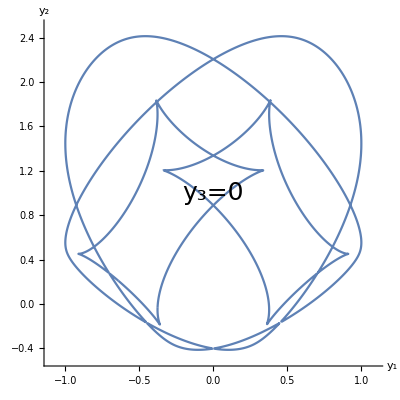

```mathematica
(* Plotting section  *)
poly2 =Factor[Quq][[5]];
plot=ContourPlot[poly2==0,{Y1,-1.1,1.1},{Y2,-0.5,2.5},Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, MaxRecursion->4,Epilog->{Text[Style[StringForm["y_3=0"],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```

```mathematica
(* points from the plot *)
points=Cases[Normal@plot,Line[pts_,___]:>pts,Infinity];
list=Flatten[points,1];
```

```mathematica
(* shifting the points so that polar coordinates from the point inside map it properly (assessed visually) *)
xdiff=0;
ydiff=1;
pts=list+ConstantArray[{-xdiff,-ydiff},Length[list]];
```

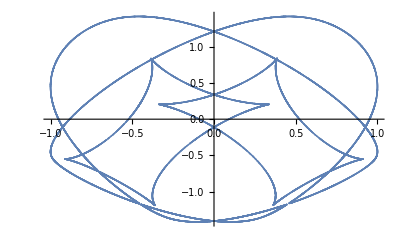

```mathematica
ListPlot[pts]
```

```mathematica
(* going to polar coordinates *)
r=Norm/@pts;
phi=(ArcTan@@#1)&/@pts;
d=0.01; (* threshold angle *)
(* function: max r s.t. exist a point on a ray alpha in pts *)
rad[alpha_]:=Max[MapThread[If[#1≤d,r[[#2]],0]&,{Abs[phi-alpha],Range[1,Length[phi]]}]];
```

```mathematica
(* ranges of phis, and corresponding Rs *)
phis1=Range[-Pi,Pi,0.01];
rs1=rad/@phis1;
```

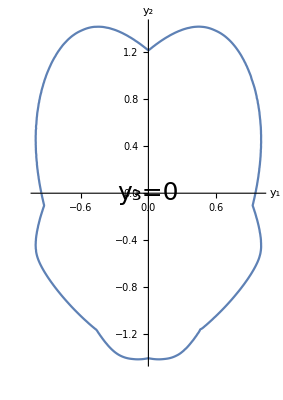

```mathematica
(* plotting in polar coordinates *)
ListPolarPlot[Transpose[{phis1,rs1}],Joined->True,Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, Epilog->{Text[Style[StringForm["y_3=0"],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```

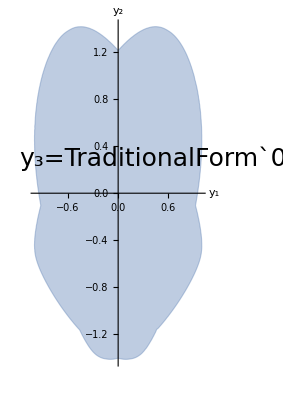

```mathematica
(*plotting with filling*)ListPolarPlot[Transpose[{phis1,rs1}],Joined->True,Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black,20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]},Epilog->{Text[Style[StringForm["y_3=`1`",0],25],Scaled[{0.7,0.6}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]/.Line->({Opacity[0.4],-Graphics-,EdgeForm[{Thick,-Graphics-}],Polygon@#1}&)
```